```mathematica
runs = {}
popsize=10000;
mutrate1={.000000390625,.000001562,.00000625,.000025,.0001,.0004,0.0016,0.0064};
mutrate2={.0000000390625,.0000001562,.000000625,.0000025,.00001,.00004,0.00016,0.00064};
generations={1000000,500000,300000,150000,80000,40000,20000,10000};
DFE1=ExponentialDistribution[1/.01];
DFE2=ExponentialDistribution[1/.01];
pop=Table[{0.,{},{}},{popsize}];
```

```mathematica
Do[
Do[
Do[(*mutation*)
If[RandomReal[]<mutrate1[[j]],
mu=RandomVariate[DFE1];
pop[[i,1]]+=mu;
AppendTo[pop[[i,2]],mu]
];
If[RandomReal[]<mutrate2[[j]],
mu=RandomVariate[DFE2];
pop[[i,1]]+=mu;
AppendTo[pop[[i,3]],mu]
],
{i,Length[pop]}];
(*sampling*)
pop=RandomChoice[E^pop[[All,1]]->pop,Length[pop]],
{generations[[j]]}];
runs=AppendTo[runs,{popsize, mutrate1[[j]],mutrate2[[j]],generations[[j]],Intersection@@pop[[All,2]]//Length,Intersection@@pop[[All,3]]//Length}];
,{j,Length[generations]}];
```

```mathematica
PDF[ExponentialDistribution[1/.01]]
```

```mathematica
NIntegrate[100. ⅇ^(-100. s)(1-ⅇ^(-2 s))/(1-ⅇ^(-2 10000 s)),{s,0,∞}]
```

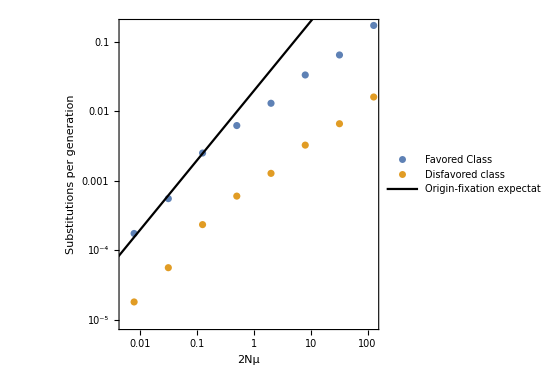

```mathematica
Show[ListLogLogPlot[
{2Table[{runs[[i,1]]runs[[i,2]],runs[[i,5]]/runs[[i,4]]},{i, Length[runs]}],
2 Table[{runs[[i,1]]runs[[i,2]],runs[[i,6]]/runs[[i,4]]},{i, Length[runs]}]},PlotLabels->Automatic,AspectRatio->Automatic,Frame->True, FrameLabel->{"2Nμ","Substitutions per generation"},PlotLegends->{"Favored Class","Disfavored class"}],
LogLogPlot[0.019684408345271964x,{x,.00001,500},PlotStyle->Black,PlotLegends->{"Origin-fixation expectation (favored class)"}]
]
```

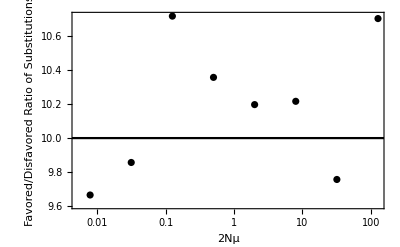

```mathematica
Show[ListLogLinearPlot[
Table[{2runs[[i,1]]runs[[i,2]],runs[[i,5]]/runs[[i,6]]},{i, Length[runs]}],Frame->True, FrameLabel->{"2Nμ","Favored/Disfavored Ratio of Substitutions"},PlotStyle->Black],
LogLinearPlot[10,{x,.00001,1000},PlotStyle->Black]
]
```